```mathematica
ClearAll["Global`*"]
```

## Shared parameters

#### Parameters

```mathematica
params2 =  {
	acapCO2-> 1.33 *10^-5 ,
	a0->0.2173,
	a1->0.224, 
	a2->0.282, 
	a3->0.2763,
	tau1->394.4 ,tau2->36.54 ,tau3->4.304 , 
	acapCH4-> 3.88*10^-4,
	tauCH4-> 11.8, 
	f1->0.37,
	f2-> 0.106
	};
```

#### Temperature response function from Caldeira and Myhrvold (2013)

```mathematica
tCumuResponseFraction2Exp = (theta0*Exp[-t/tau0] + theta1*Exp[-t/tau1]);
climateResponseCM2013 = -1* eff * D[tCumuResponseFraction2Exp, t] /.{eff->6.70/6.79, theta0->0.551, tau0->3.62, theta1->0.449, tau1->219.0}//Simplify;
```

## CH4

#### Radiative forcing for a pulse emission

```mathematica
rfCh4 = (acapCH4 ⅇ^(-t/tauCH4) (1+f1+f2))//Simplify;
rfCh4Unit = (rfCh4 / (rfCh4/.t->0))/.t->dist;
emisCh4Case1 = 1;
rfCh4Case1 = Integrate[(rfCh4Unit * emisCh4Case1), {dist, 0, t}]/.params2//Simplify;
(*emisCh4Case2 = 1.01^t/.t->t-dist;*)
emisCh4Case2 = t/.t->t-dist;
rfCh4Case2 = Integrate[(rfCh4Unit * emisCh4Case2), {dist, 0, t}]/.params2//Simplify;
```

```mathematica
term1ClimateResponseCM2013 = climateResponseCM2013/.{t->H-t};
agtpCh4Case1 = Integrate[term1ClimateResponseCM2013 * rfCh4Case1, {t, 0, H}]//Simplify;
agtpCh4Case2 = Integrate[term1ClimateResponseCM2013 * rfCh4Case2, {t, 0, H}]//Simplify;
rowCh4Case1 = D[agtpCh4Case1, H]//Simplify;
rowCh4Case2 = D[agtpCh4Case2, H]//Simplify;
```

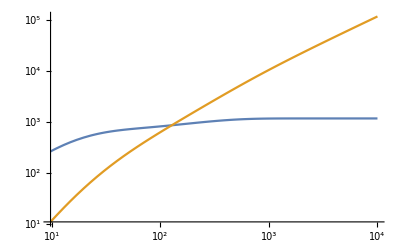

```mathematica
Plot[ {agtpCh4Case1*100, agtpCh4Case2}, {H, 0, 10000}, PlotRange->All, PlotStyle->{blue, red}, ScalingFunctions -> {"Log10", "Log10"}]
```

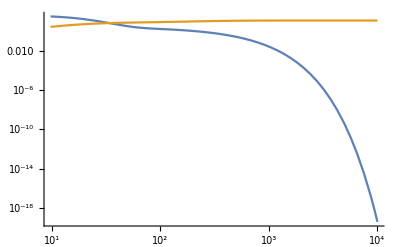

```mathematica
Plot[ {rowCh4Case1*100, rowCh4Case2}, {H, 0, 10000}, PlotRange->All, PlotStyle->{blue, red}, ScalingFunctions -> {"Log10", "Log10"}]
```

## CO2

#### Forcing response per unit emission

```mathematica
rfCo2 = (acapCO2 (a0+a1 ⅇ^(-t/tau1)+a2 ⅇ^(-t/tau2)+a3 ⅇ^(-t/tau3)))//Simplify;
rfCo2Unit = (rfCo2 / (rfCo2/.t->0))/.t->dist//Simplify;
emisCo2Case1 = 1;
rfCo2Case1 = Integrate[(rfCo2Unit * emisCo2Case1), {dist, 0, t}]/.params2//Simplify;
(*emisCh4Case2 = 1.01^t/.t->t-dist;*)
emisCo2Case2 = t/.t->t-dist;
rfCo2Case2 = Integrate[(rfCo2Unit * emisCo2Case2), {dist, 0, t}]/.params2//Simplify;
```

```mathematica
term1ClimateResponseCM2013 = climateResponseCM2013/.{t->H-t};
agtpCo2Case1 = Integrate[term1ClimateResponseCM2013 * rfCo2Case1, {t, 0, H}]//Simplify;
agtpCo2Case2 = Integrate[term1ClimateResponseCM2013 * rfCo2Case2, {t, 0, H}]//Simplify;
rowCo2Case1 = D[agtpCo2Case1, H]//Simplify;
rowCo2Case2 = D[agtpCo2Case2, H]//Simplify;
```

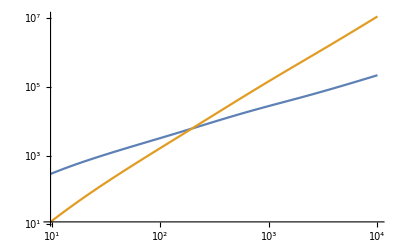

```mathematica
Plot[ {agtpCo2Case1*100, agtpCo2Case2}, {H, 0, 10000}, PlotRange->All, PlotStyle->{blue, red}, ScalingFunctions -> {"Log10", "Log10"}]
```

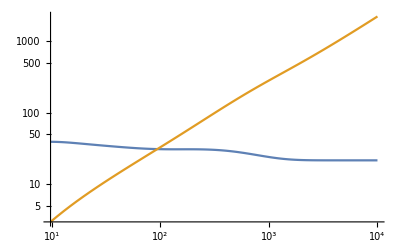

```mathematica
Plot[ {rowCo2Case1*100, rowCo2Case2}, {H, 0, 10000}, PlotRange->All, PlotStyle->{blue, red}, ScalingFunctions -> {"Log10", "Log10"}]
```